# Simple Harmonic Motion

## PreLab submission with a pass grade is required to begin the lab. Must be submitted no later than right before the start of the lab.

Name: Aryan Malhotra
Section: H4
Date: 11/05/2024

## Readings

You can review the concepts using Wikipedia or your favorite textbook,
Simple Harmonic Motion, Error Propagation Rules

Review the least-squares fitting using Chapter 8 of John R Taylor's book or the shorter version given in Lab 3, Readings section.

### Spring Force

Mathematically, the restoring force exerted by a spring, stretched from length l_0 to a length l, is given by Hooke’s law, 
F=-k(l - l_0),
where the constant k, called the spring constant, characterizes the stiffness of the spring. A large k means a large force is needed to stretch (or compress) the spring a certain distance.
When the spring is relaxed at length l_0 the exerted force is zero.

If there is a mass hanging from the spring, the two forces acting on the mass must add up to zero in order to have equilibrium. This means,
m g - k(l - l_0) = 0.

## Dialog:

To find the spring constant of a spring, a student loads it with various masses m and measures the corresponding lengths l. Her results are shown in the table above. Because the force mg=k(l-l0), where l0 is the unstretched length of the spring, these data should fit a straight line, l=l0+(g/k)m.
- Save the data in a two column format [you can use Insert Table from the top menu].
- Make least-squares fit to this line for the given data, and find the best estimates for the unstretched length l0 and the spring constant k.
- Check your answers using the LinearModelFit functions in Mathematica.
- Find the uncertainty in the g/k constant and then use the error propagation rules to find the uncertainty in the k constant.

```mathematica
data ={{200, 300, 400, 500, 600, 700, 800, 900}, {5.1, 5.5, 5.9, 6.8, 7.4, 7.5, 8.6, 9.4}}
```

200 | 300 | 400 | 500 | 600 | 700 | 800 | 900
5.1 | 5.5 | 5.9 | 6.8 | 7.4 | 7.5 | 8.6 | 9.4

```mathematica
loads =0.001* data[[All,1]][[1]]
lengths = 0.01*data[[All,2]][[1]]
```

{0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9}

{0.051,0.055,0.059,0.068,0.074,0.075,0.086,0.094}

```mathematica
num=Length[loads];
sumx=Sum[loads[[x]],{x,1,num}];
sumy=Sum[lengths[[y]],{y,1,num}];
sumx2=Sum[loads[[x]]^2,{x,1,num}];
sumxy=Sum[loads[[x]]*lengths[[x]],{x,1,num}];

del=num*sumx2-sumx^2;

B=(num*sumxy-sumx*sumy)/del
A=(sumx2*sumy-sumx*sumxy)/del
l0 = A
k = 9.81/B
```

0.0607143

0.0368571

0.0368571

161.576

LINEAR FIT MODEL
y = A + Bx ⟺l=l0+(g/k)m
hence, l0 = A & g/k = B
⇒ y = 0.369 + 0.0607x
y = length
x = load

```mathematica
lm=LinearModelFit[Transpose[{loads,lengths}],x,x]
```

FittedModel[…]

```mathematica
standardError = Sqrt[1/(num-2) * Sum[(lengths[[i]] - A - B*loads[[i]])^2 ,{i,1,num}]]

(*Calculate uncertainty in B*)
meanLoad=Mean[loads];
sumXSquared=Total[(loads-meanLoad)^2];
sigmaB=standardError/Sqrt[sumXSquared];

g=9.81

(*Propagate uncertainty to find uncertainty in k*)
sigmaK=(g/B^2)*sigmaB;
sigmaA = sigmay*Sqrt[sumx2/del];
{A, sigmaA, B,sigmaB,k,sigmaK}
```

0.00242507

9.81

{0.0368571,0.00222953,0.0607143,0.00374196,161.576,9.95833}

## Results

- Record your results in the table below.

```mathematica
Grid[{{Text["Simple Harmonic Motion"],SpanFromLeft},{"l0 (Mathematica), m","l0 (calculated), m","Δl0(calculated), m","k (Mathematica), N/m","k (calculated), N/m","Δk (calculated), N/m"},{0.0369,0.0369,NumberForm[sigmaA, 3],NumberForm[k,4],NumberForm[k,4],NumberForm[sigmaK,4]}},Frame->All]
```

Simple Harmonic Motion |  |  |  |  | 
l0 (Mathematica), m | l0 (calculated), m | Δl0(calculated), m | k (Mathematica), N/m | k (calculated), N/m | Δk (calculated), N/m
0.0369 | 0.0369 | 0.00223 | 161.6 | 161.6 | 9.958

- Use the example below to plot the data with error bars. sigmay is the uncertainty in the measured length values that you calculated from Eq. 8.15 in Taylor's Chapter 8.
In the code below, the data is not complete and sigmay is not defined. So fix it based on your needs.

FittedModel[…]

| Estimate | Standard Error | Confidence Interval
1 | 0.0368571 | 0.00222953 | {0.0314017,0.0423126}
x | 0.0607143 | 0.00374196 | {0.051558,0.0698705}

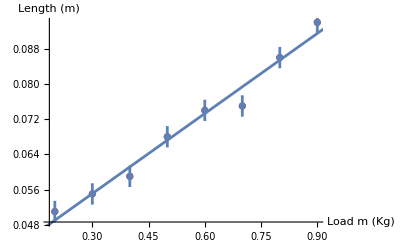

```mathematica
Needs["ErrorBarPlots`"];
data=Transpose[{loads,lengths}];
sigmay=  sigmay  ;
line = LinearModelFit[data,x,x]
line["ParameterConfidenceIntervalTable"]
Show[
ListPlot[data, PlotStyle->Red],
Plot[line[x], {x, 0, 5}],
ErrorListPlot[Join[data,Table[{sigmay},{i,1,Length[data]}],2]],
AxesLabel->{"Load m (Kg)","Length (m)"}]
```

This error bar plot represents our data set and the linear fit model (least squares) which happens to match with a fairly low error.

Rutgers 275 Classical Physics Lab
“Simple Harmonic Motion”
Contributed by Maryam Taherinejad and Girsh Blumberg ©2014